# AffineCipher

Encipher a string using the affine cipher

## Definition

```mathematica
ClearAll[iAffineCipherAlphabetSmall,iAffineCipherAlphabetLarge,AffineCipher]
iAffineCipherAlphabetSmall=Thread[CharacterRange["a","z"]->Range[0,25]];
iAffineCipherAlphabetLarge=Thread[CharacterRange["A","Z"]->Range[0,25]];
AffineCipher::anotcoprime = "The value for a, `1`, is not coprime with the alphabet length (26).";
AffineCipher[x:(_String|{___String}),{a_Integer,b_Integer}]:=Module[{repsmall,replarge,reps,m=26,rev},
If[CoprimeQ[a,26],
repsmall =rev=iAffineCipherAlphabetSmall;
rev=Reverse/@rev;
repsmall[[All,2]]=Mod[a repsmall[[All,2]]+b,m]/.rev;

replarge =rev=iAffineCipherAlphabetLarge;
rev=Reverse/@rev;
replarge[[All,2]]=Mod[a replarge[[All,2]]+b,m]/.rev;

reps=Join[repsmall,replarge];

StringReplace[x,reps]
,
Message[AffineCipher::anotcoprime,a];
$Failed
]
]
AffineCipher[{a_Integer,b_Integer}][x_]:=AffineCipher[x,{a,b}]
```

## Documentation

### Usage

AffineCipher[string,{a,b}]

enciphers string using the affine cipher with parameters a and b.

AffineCipher[{a,b}]

represents an operator form of AffineCipher that can be applied to an expression.

### Details & Options

For the affine cipher, the letters "a"–"z" are numbered 0–25. Each character in string is converted to a number x using the aforementioned numbering. Each number is then transformed by computing (ax+b)mod26. The new numbers are then reinterpreted as letters.

Here is an example enciphering the letters "A"–"Z" for a=5 and b=8. Deciphering is done by reading the diagram from bottom to top.

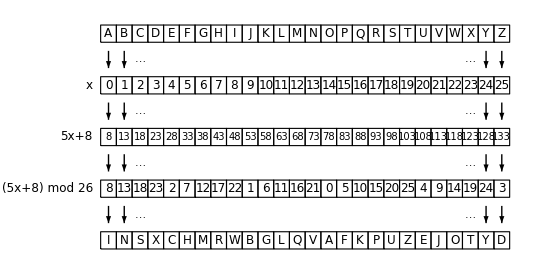

The case of the letters is retained by AffineCipher.

## Examples

### Basic Examples

Convert a simple text:

```mathematica
AffineCipher["affine cipher",{5,8}]
```

ihhwvc swfrcp

### Scope

AffineCipher automatically threads over a list of strings:

```mathematica
AffineCipher[{"this","is","a","test"},{5,8}]
```

{zrwu,wu,i,zcuz}

Create an operator:

```mathematica
op=AffineCipher[{5,8}]
```

AffineCipher[{5,8}]

Apply the operator to a string:

```mathematica
op["balloon"]
```

nillaav

### Properties and Relations

The Caesar cipher can be recreated using the affine cipher by choosing a=1:

```mathematica
string="This is just a test";
{AffineCipher[string,{1,8}],ResourceFunction["CaesarCipher"][string,8]}
```

{Bpqa qa rcab i bmab,Bpqa qa rcab i bmab}

### Possible Issues

The parameter a must be coprime with 26:

```mathematica
AffineCipher["Mathematica",{4,2}]
```

AffineCipher::anotcoprime: The value for a, 4, is coprime with the alphabet length (26).

$Failed

Some of the permissible values for a are:

```mathematica
Select[Range[100],CoprimeQ[#,26]&]
```

{1,3,5,7,9,11,15,17,19,21,23,25,27,29,31,33,35,37,41,43,45,47,49,51,53,55,57,59,61,63,67,69,71,73,75,77,79,81,83,85,87,89,93,95,97,99}

Strings using numbers or letters with diacritics are not converted:

```mathematica
AffineCipher["It was Chloë who opened the 2 piñatas",{5,8}]
```

Wz oiu Srlaë ora afcvcx zrc 2 fwñiziu

Use RemoveDiacritics, StringDelete, IntegerName and ToLowerCase to transform the message:

```mathematica
string=StringReplace[ToLowerCase[StringDelete[RemoveDiacritics["It was Chloë who opened the 2 piñatas"]," "]],r:Longest[DigitCharacter ..]:>IntegerName[ToExpression@r]]
```

itwaschloewhoopenedthetwopinatas

Now the transformed message can be enciphered:

```mathematica
AffineCipher[string,{5,8}]
```

wzoiusrlacoraafcvcxzrczoafwviziu

## Source & Additional Information

### Contributed By

Sander Huisman

### Keywords

affine cipher

substitution cipher

monoalphabetic substitution cipher

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

Encrypt

Decrypt

Hash

StringReplace

### Related Resource Objects

CaesarCipher

VigenereCipher

AtbashCipher

PigpenCipher

RailFenceCipher

### Source/Reference Citation

Source, reference or citation information

### Links

Wikipedia–Affine Cipher

### Tests

```mathematica
VerificationTest[AffineCipher["affinecipher",{5,8}],"ihhwvcswfrcp"]
VerificationTest[AffineCipher["affinecipher",{13,8}],$Failed,{AffineCipher::anotcoprime}]
```

TestResultObject[…]

TestResultObject[…]

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.